```mathematica
hepData=Import["/Users/samiyrjanheikki/Downloads/HEPData-ins617784-v1-csv/Table1.csv"];
pT=hepData[[All,1]];
σ=hepData[[All,4]];
constant=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/constant_pT.csv"];
pT2=constant[[All,1]];
σ2=constant[[All,2]];
nonconstant=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/nonconstant_pT.csv"];
pT3=constant[[All,1]];
σ3=constant[[All,2]];
```

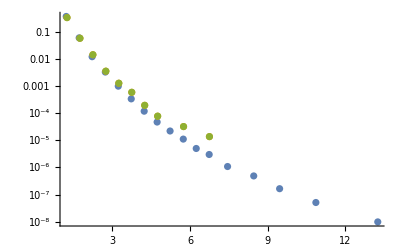

```mathematica
plot=Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT2,σ2}],PlotStyle->ColorData[97,"ColorList"][[2]]],ListLogPlot[Transpose[{pT3,σ3}],PlotStyle->ColorData[97,"ColorList"][[3]]],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma.pdf",plot]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma.pdf